### Testing new fitness functions

#### Density of output cells to 1 /Pi

```mathematica
Module[
{deep=100,cut=200,ru,life},
SeedRandom[426778];
{{"[◼]", "RulesMutationPlot"}}[
Take[First/@Split[First/@NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep]
],{48,50}]]]
```

```mathematica
{{"[◼]", "RandomRuleMutation"}}[initru]
```

{1871834567,2,2}

```mathematica
initru
```

{1872096711,2,2}

```mathematica
inits
```

{0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,1,0,0,1,1,0,1,1,1,1,0,0,1,1,1,1,1,0,0,0,0,0,1,1,1,0,0,1,1,0,1,0,0,0,1,0,1,0,1,0,1,0,0,1,1,1,1,0,1,0,1,0,1,0,1,1,1,0,0,1,1,1,1,0,0,0,1,1,0,0,0,1,1,1,1,0,1,1,0,0,0,0,1,1,1,0,1,1,0,0,0,1,0,1,1,0,1,0,0,1,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,0,0,1,1,1,1,0,0,0,0,0,1,0,0,0,1,1,1,0,1,0,0,1,1,1,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,1,1,1,0,0,1,1,0,1,0,1,0,1,1,1,1,1,0,0,0,0,1,0,0,1,1,0,1,0,0,0,1,1,1,0,0,1,0,0,1,0,1,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,0,0,1,0,1,1,0,1,0,0,0,1,1,1,1,1,0,1,0,1,1,1,0,0,0,1,1,0,0,0,1,1,1,0,1,1,0,0,1,1,0,1,1,1,0,1,1,1,1,0,0,0,0,1}

```mathematica
evo = Module[
{deep = 4000(*,initru, nru, nfit, inits*)},
SeedRandom[3432111];
inits = RandomInteger[1, 200];
initru = {ResourceFunction["RandomCA"][{2, 2},"Quiescent"->True]["RuleNumber"], 2, 2};
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
nfit =Abs[( 1 / Pi )- Count[CellularAutomaton[nru, inits, {{{120}}}], 1]/300];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]];
```

```mathematica
ArrayPlot[CellularAutomaton[#,inits, 120]]&/@ GatherBy[evo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

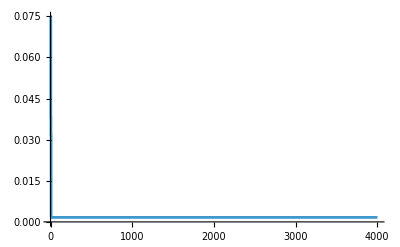

```mathematica
ListStepPlot[evo[[All, -1]]]
```

#### With changing initial conditions

```mathematica
evo = Module[
{deep = 4000(*,initru, nru, nfit, inits*)},
SeedRandom[3432112];
inits = RandomInteger[1, 200];
initru = {ResourceFunction["RandomCA"][{2, 2},"Quiescent"->True]["RuleNumber"], 2, 2};
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
nfit =Abs[( 1 / Pi )- Count[CellularAutomaton[nru, RandomInteger[1, 200], {{{120}}}], 1]/300];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]];
```

```mathematica
ArrayPlot[CellularAutomaton[#,inits, 120]]&/@ GatherBy[evo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

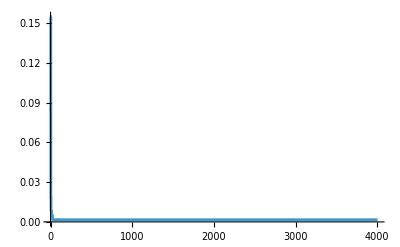

```mathematica
ListStepPlot[evo[[All, -1]]]
```

#### More runs of changing initial conditions

```mathematica
evos = 
ParallelTable[Module[
{deep = 4000(*,initru, nru, nfit, inits*)},
SeedRandom[3432113 + i];
inits = RandomInteger[1, 200];
initru = {ResourceFunction["RandomCA"][{2, 2},"Quiescent"->True]["RuleNumber"], 2, 2};
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
nfit =Abs[( 1 / Pi )- Count[CellularAutomaton[nru, RandomInteger[1, 200], {{{120}}}], 1]/200];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]], {i, 10}];
```

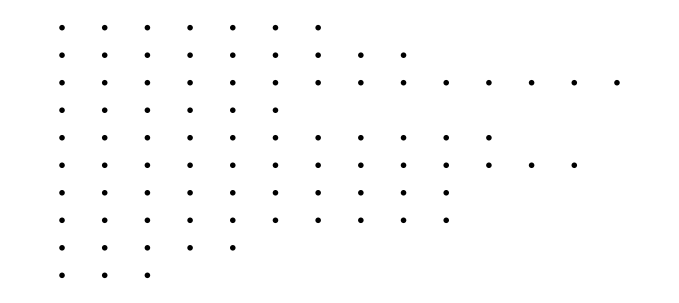

```mathematica
GraphicsGrid[ArrayPlot[CellularAutomaton[#,inits, 120], ImageSize->100]&/@ GatherBy[#, Last][[All, 1, 1]]&/@ evos]
```

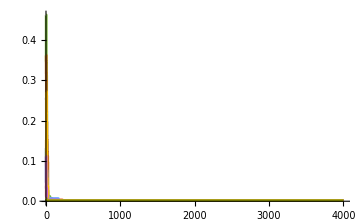

```mathematica
ListStepPlot[evos[[All, All, -1]]]
```

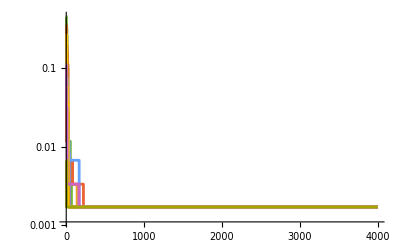

```mathematica
ListStepPlot[evos[[All, All, -1]], ScalingFunctions->"Log"]
```

```mathematica
GatherBy[evos[[1]], Last][[-1, 1, 1]]
```

{2818655860,2,2}

```mathematica
Table[SeedRandom[333222 + i];ArrayPlot[CellularAutomaton[GatherBy[evos[[1]], Last][[-1, 1, 1]], RandomInteger[1, 200], 120],ImageSize->150], {i, 10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
N[1 / Pi]
```

0.31831

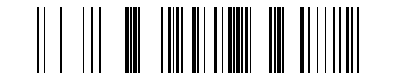
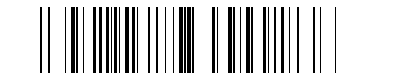
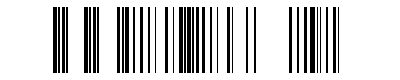
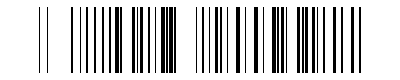
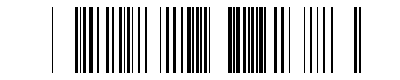
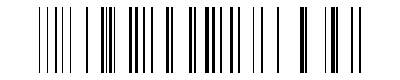
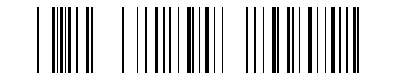
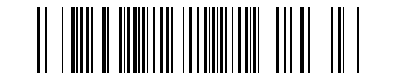
{-Graphics-0.26,-Graphics-0.265,-Graphics-0.28,-Graphics-0.29,-Graphics-0.31,-Graphics-0.22,-Graphics-0.25,-Graphics-0.33,-Graphics-0.185,-Graphics-0.285}

```mathematica
Table[SeedRandom[333222 + i];
With[{caf = CellularAutomaton[GatherBy[evos[[1]], Last][[-1, 1, 1]], RandomInteger[1, 200], {{120}}]},Labeled[ArrayPlot[caf,ImageSize-> {400, Automatic}], Text[N[Count[First[caf], 1] / 200]]]], {i, 10}]
```

Effectiveness from different random initial conditions along the way

#### Multiple initial conditions at each step

```mathematica
evos = 
ParallelTable[Module[
{deep = 4000(*,initru, nru, nfit, inits*)},
SeedRandom[3432113 + i];
inits = RandomInteger[1, 200];
initru = {ResourceFunction["RandomCA"][{2, 2},"Quiescent"->True]["RuleNumber"], 2, 2};
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
nfit =Max[Abs[( 1 / Pi )- Count[CellularAutomaton[nru, #, {{{120}}}], 1]/200]&/@ RandomInteger[1, {5, 200}]];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]], {i, 10}];
```

### Longer and longer periods

```mathematica
evos = 
Module[
{deep = 4000(*,initru, nru, nfit, inits*)},
SeedRandom[3432113 + i];
inits = RandomInteger[1, 200];
initru = {ResourceFunction["RandomCA"][{2, 2},"Quiescent"->True]["RuleNumber"], 2, 2};
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
nfit =Max[Abs[( 1 / Pi )- Count[CellularAutomaton[nru, #, {{{120}}}], 1]/200]&/@ RandomInteger[1, {200, 5}]];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]];
```

### Approximating sin wave with density

```mathematica
Table[1/2Sin[i/5.5]+1/2, {i, 1, 120}]
```

{0.590409,0.677838,0.759403,0.832417,0.894473,0.943523,0.977953,0.996625,0.998926,0.984778,0.954649,0.909531,0.850913,0.780725,0.701284,0.615206,0.525331,0.43462,0.346065,0.262585,0.186931,0.121599,0.0687408,0.0301001,0.00695061,0.0000553805,0.00964176,0.0353937,0.0764623,0.131494,0.198673,0.275787,0.360292,0.449403,0.540182,0.629636,0.714817,0.792916,0.861358,0.917887,0.96064,0.988207,0.99968,0.994679,0.973371,0.936457,0.885154,0.821154,0.746566,0.66385,0.575733,0.485118,0.394995,0.308333,0.227989,0.156613,0.0965579,0.0498025,0.0178887,0.00186868,0.00227046,0.0190808,0.0517456,0.0991879,0.159844,0.231714,0.312428,0.399326,0.489543,0.580104,0.668025,0.750407,0.824533,0.887961,0.938599,0.974777,0.995304,0.999502,0.987233,0.958901,0.915441,0.858285,0.789318,0.710812,0.625357,0.535769,0.445002,0.356048,0.27184,0.195154,0.128517,0.0741268,0.0337764,0.00879604,9.0972×10^-6,0.00770529,0.0316309,0.0709972,0.124506,0.190394,0.266489,0.350282,0.439011,0.52975,0.619508,0.705327,0.784377,0.854051,0.912054,0.956473,0.985843,0.999196,0.996092,0.976634,0.941463,0.891738,0.829098,0.75561,0.673694,0.586053}

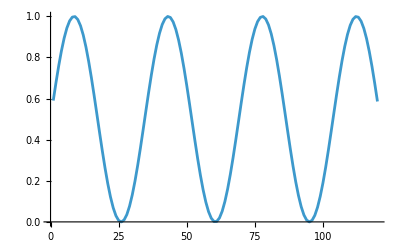

```mathematica
ListLinePlot[Table[1/2Sin[i/5.5]+1/2, {i, 1, 120}]]
```

```mathematica
sevo = Module[
{deep = 4000, width = 200, length = 120(*,initru, nru, nfit, inits*)},
SeedRandom[3532113];
initru = {ResourceFunction["RandomCA"][{2, 2},"Quiescent"->True]["RuleNumber"], 2, 2};
sc = Table[1/2Sin[i/5.5]+1/2, {i, 1, 121}];
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
nfit =Total[MapIndexed[Abs[sc[[First[#2]]]- Count[#, 1]/200]&, CellularAutomaton[nru, RandomInteger[1, width], length]]];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]];
```

```mathematica
ArrayPlot[CellularAutomaton[#,RandomInteger[1, 200], 120]]&/@ GatherBy[sevo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

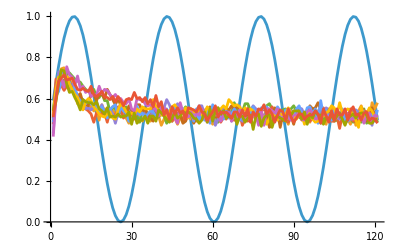

```mathematica
ListLinePlot[Prepend[Table[Count[#, 1]/200&/@CellularAutomaton[GatherBy[sevo, Last][[-1, 1, 1]],RandomInteger[1, 200], 120], 10], sc], PlotRange->All]
```

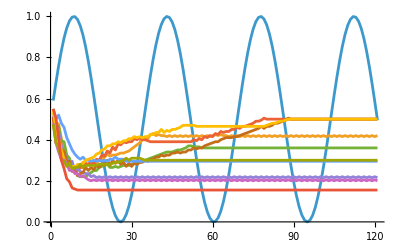
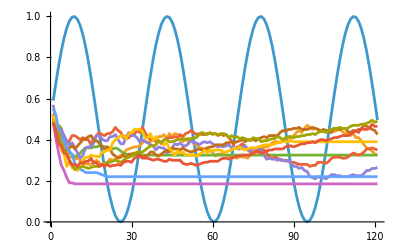
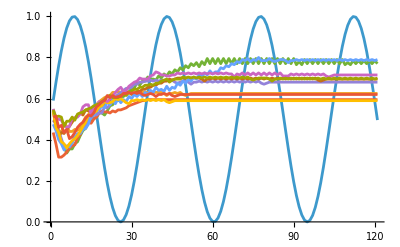
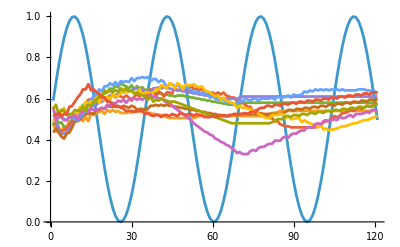
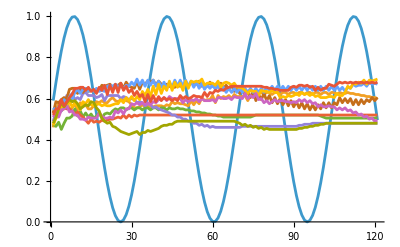
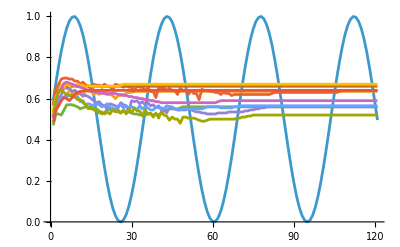
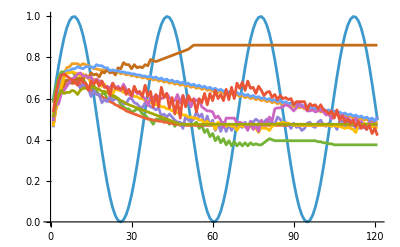
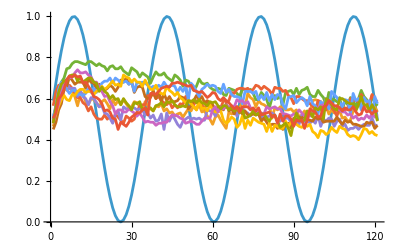

```mathematica
ListLinePlot[Prepend[Table[Count[#, 1]/200&/@CellularAutomaton[#,RandomInteger[1, 200], 120], 10], sc], PlotRange->All]&/@ GatherBy[sevo, Last][[All, 1, 1]]
```

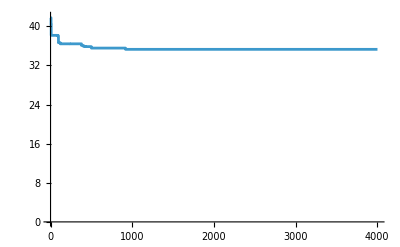

```mathematica
ListStepPlot[sevo[[All, -1]], PlotRange->42]
```

#### From single random initial condition

```mathematica
sevo = Module[
{deep = 4000, width = 200, length = 120(*,initru, nru, nfit, inits*)},
SeedRandom[3532114];
initru = {ResourceFunction["RandomCA"][{2, 2},"Quiescent"->True]["RuleNumber"], 2, 2};
inits = RandomInteger[1, width];
sc = Table[1/2Sin[i/5.5]+1/2, {i, 1, 121}];
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
nfit =Total[MapIndexed[Abs[sc[[First[#2]]]- Count[#, 1]/200]&, CellularAutomaton[nru, inits, length]]];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]];
```

```mathematica
ArrayPlot[CellularAutomaton[#,inits, 120]]&/@ GatherBy[sevo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

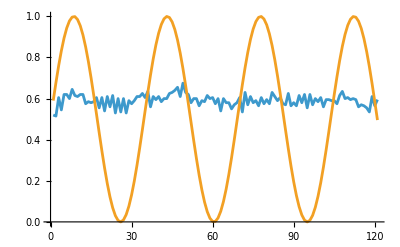

```mathematica
ListLinePlot[{Count[#, 1]/200&/@CellularAutomaton[GatherBy[sevo, Last][[-1, 1, 1]],inits, 120], sc}, PlotRange->All]
```

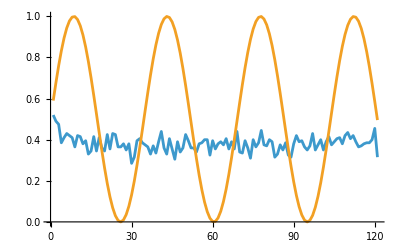
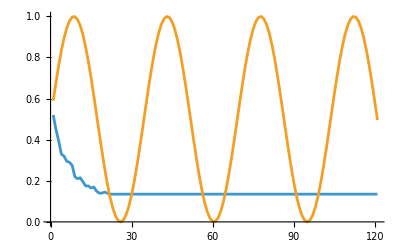
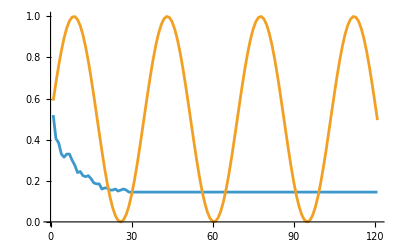
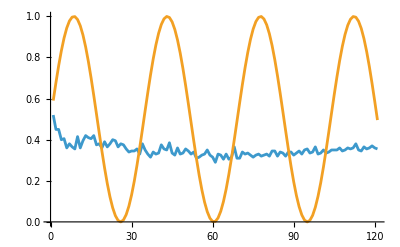
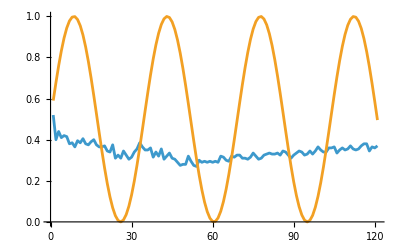
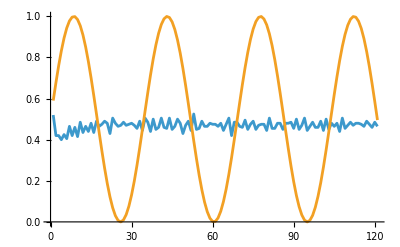
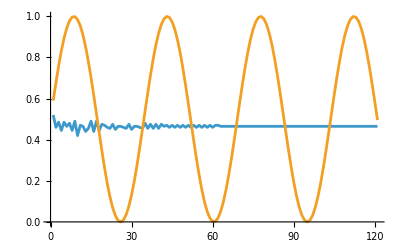
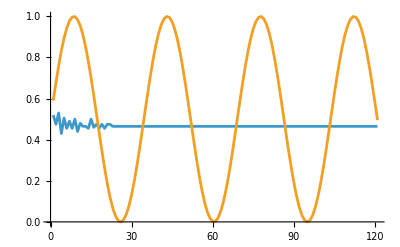
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[{N[Count[#, 1]/200]&/@CellularAutomaton[#,inits, 120], sc}]&/@ GatherBy[sevo, Last][[All, 1, 1]]
```

```mathematica
ListStepPlot[sevo[[All, -1]], PlotRange->42]
```

-Graphics-

#### Simpler sin curve

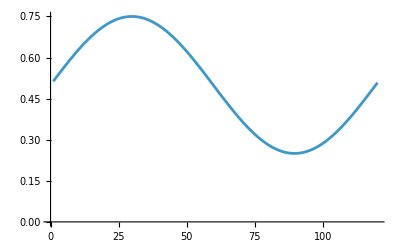

```mathematica
ListLinePlot[Table[1/4Sin[i/19]+1/2, {i, 1, 120}]]
```

```mathematica
sevo = Module[
{deep = 4000, width = 200, length = 120(*,initru, nru, nfit, inits*)},
SeedRandom[3532123];
initru = {ResourceFunction["RandomCA"][{2, 2},"Quiescent"->True]["RuleNumber"], 2, 2};
sc = Table[1/4Sin[i/19]+1/2, {i, 1, 121}];
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
nfit =Total[MapIndexed[Abs[sc[[First[#2]]]- Count[#, 1]/200]&, CellularAutomaton[nru, RandomInteger[1, width], length]]];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]];
```

```mathematica
ArrayPlot[CellularAutomaton[#,RandomInteger[1, 200], 120]]&/@ GatherBy[sevo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

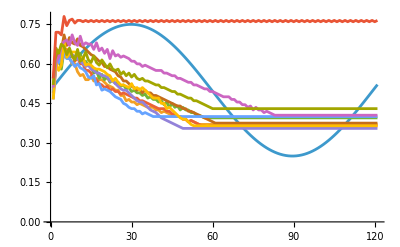

```mathematica
ListLinePlot[Prepend[Table[Count[#, 1]/200&/@CellularAutomaton[GatherBy[sevo, Last][[-1, 1, 1]],RandomInteger[1, 200], 120], 10], sc], PlotRange->All]
```

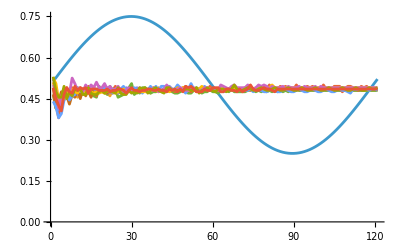
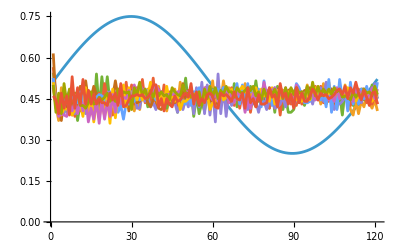
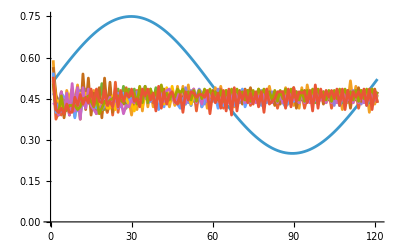
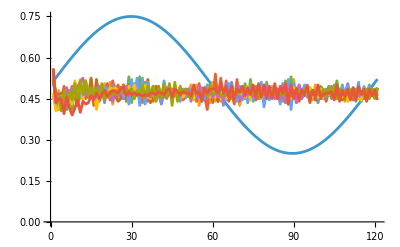
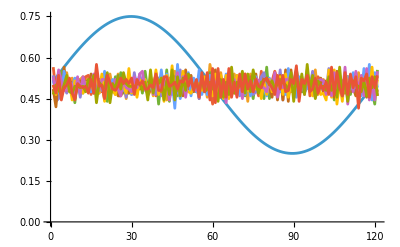
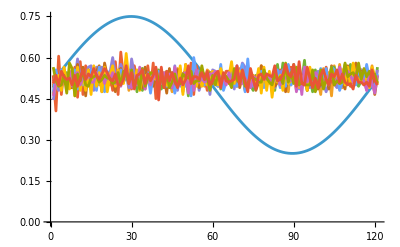
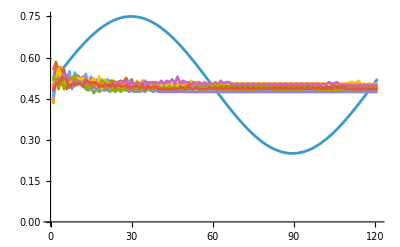
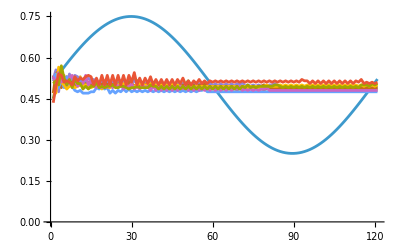

```mathematica
ListLinePlot[Prepend[Table[Count[#, 1]/200&/@CellularAutomaton[#,RandomInteger[1, 200], 120], 10], sc], PlotRange->All]&/@ GatherBy[sevo, Last][[All, 1, 1]]
```

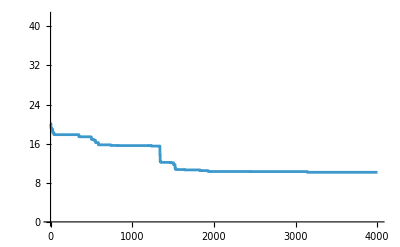

```mathematica
ListStepPlot[sevo[[All, -1]], PlotRange->42]
```

#### Without quiescence

```mathematica
sevo = Module[
{deep = 4000, width = 200, length = 120(*,initru, nru, nfit, inits*)},
SeedRandom[3532123];
initru = {ResourceFunction["RandomCA"][{2, 2}]["RuleNumber"], 2, 2};
sc = Table[1/4Sin[i/19]+1/2, {i, 1, 121}];
NestList[Function[{ru, fitness}, 
nru={FromDigits[MapAt[RandomChoice[Delete[Range[0, 1],# + 1]]&,IntegerDigits[ru[[1]],2, 2^5], RandomInteger[{1, 2^5}]], 2], 2, 2};
nfit =Total[MapIndexed[Abs[sc[[First[#2]]]- Count[#, 1]/200]&, CellularAutomaton[nru, RandomInteger[1, width], length]]];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]];
```

```mathematica
ArrayPlot[CellularAutomaton[#,RandomInteger[1, 200], 120]]&/@ GatherBy[sevo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

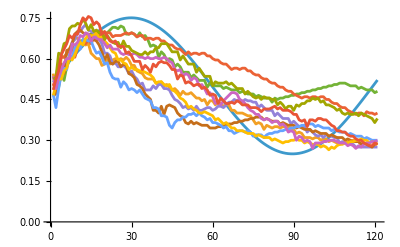

```mathematica
ListLinePlot[Prepend[Table[Count[#, 1]/200&/@CellularAutomaton[GatherBy[sevo, Last][[-1, 1, 1]],RandomInteger[1, 200], 120], 10], sc], PlotRange->All]
```

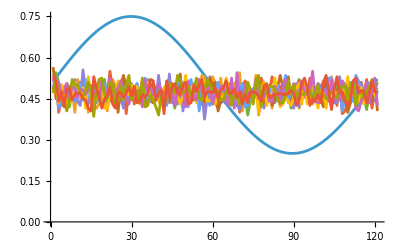
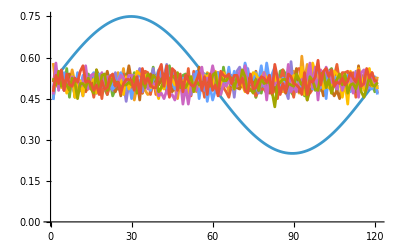
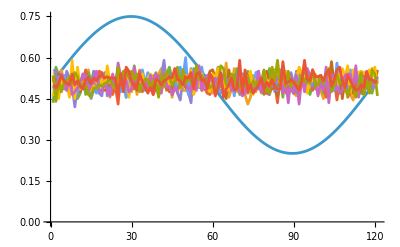
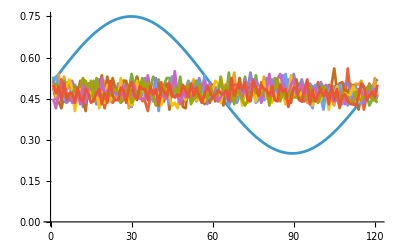
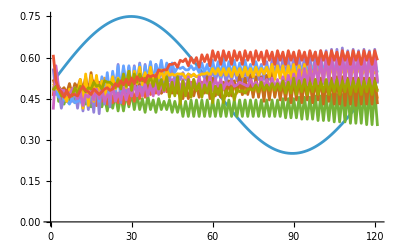
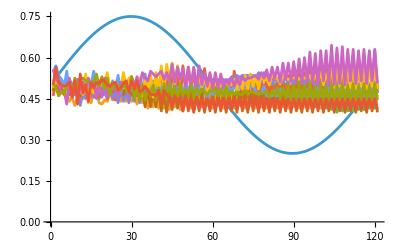
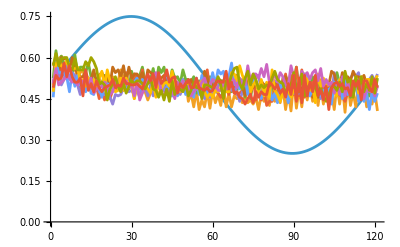
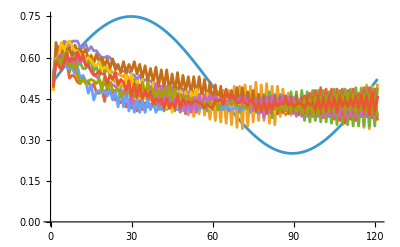

```mathematica
ListLinePlot[Prepend[Table[Count[#, 1]/200&/@CellularAutomaton[#,RandomInteger[1, 200], 120], 10], sc], PlotRange->All]&/@ GatherBy[sevo, Last][[All, 1, 1]]
```

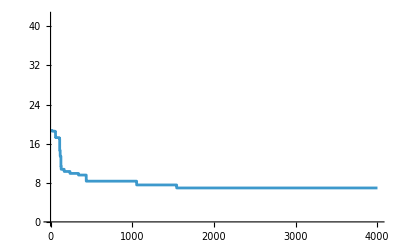

```mathematica
ListStepPlot[sevo[[All, -1]], PlotRange->42]
```

#### Single-cell sin wave non-zero range

```mathematica
Length[Table[1/10Sin[i/16]+.11 , {i, -24, 175}]]
```

200

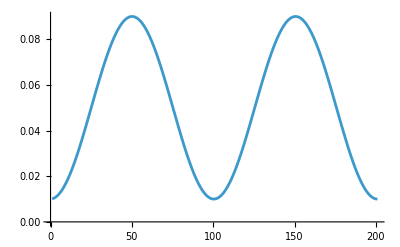

```mathematica
ListLinePlot[Table[1/25Sin[i/16] + .05, {i, -24, 176}]]
```

```mathematica
evo = Module[
{deep =100, width = 400, length = 200(*,initru, nru, nfit, inits*)},
SeedRandom[3532123];
initru = {ResourceFunction["RandomCA"][{4, 1}, "Quiescent"->True]["RuleNumber"], 4, 1};
sc = Table[1/25Sin[i/16] + .05, {i, -24, 176}];
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
nfit = Total[MapIndexed[
Function[{row, idx}, Abs[sc[[First[idx]]] - ((If[Length[#]===0,0,Last[#]-First[#]+1]&)[{{"[◼]", "nonzeroRange"}}[row]]/width)]],
CellularAutomaton[nru, CenterArray[1, width], length]]];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]];
```

```mathematica
evo = Module[
{deep =1000, width = 400, length = 200(*,initru, nru, nfit, inits*)},
SeedRandom[3532123];
initru = {ResourceFunction["RandomCA"][{4, 1}, "Quiescent"->True]["RuleNumber"], 4, 1};
sc = Table[1/25Sin[i/16] + .05, {i, -24, 176}];
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
nfit = 
Total[
MapIndexed[
Abs[sc[[First[#2]]] - (#1 / width)]&, PadRight[#[[-1, 2]] - #[[1, 2]]&/@SplitBy[SparseArray[CellularAutomaton[nru, CenterArray[1, width], length]]["ExplicitPositions"],
First], length]]];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]];
```

```mathematica
ArrayPlot[CellularAutomaton[#,CenterArray[1, 400], 200]]&/@ GatherBy[evo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

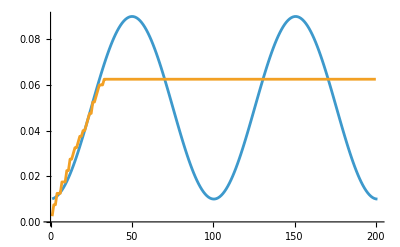

```mathematica
ListLinePlot[
Join[{sc}, {PadRight[(#[[-1, 2]] - #[[1, 2]] +1)/400&/@SplitBy[SparseArray[CellularAutomaton[GatherBy[evo, Last][[-1, 1, 1]], CenterArray[1, 400], 200]]["ExplicitPositions"],
First], 200]}]]
```

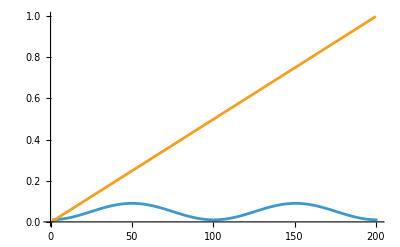
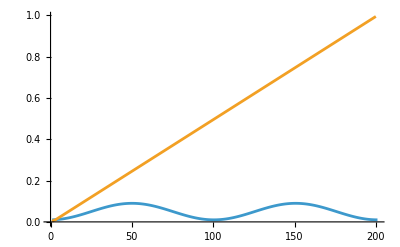
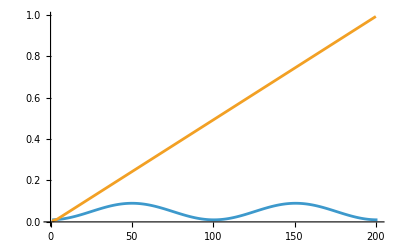
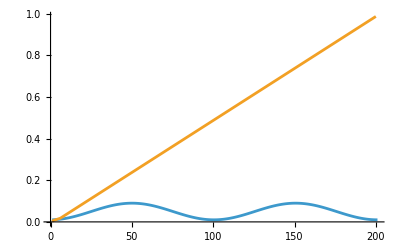
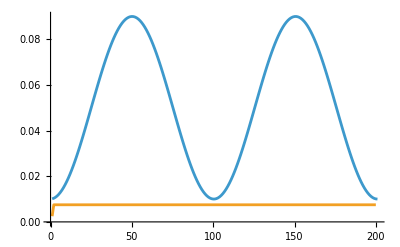
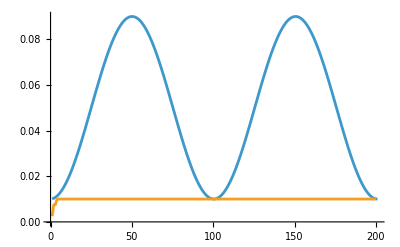
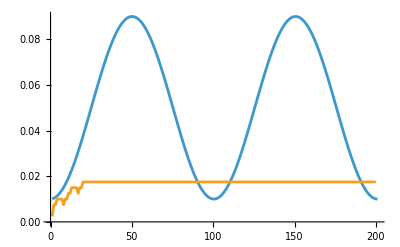
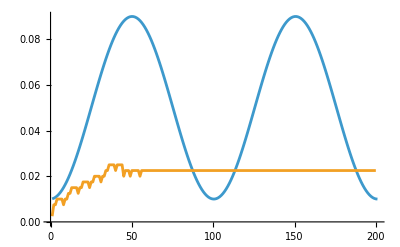
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[
Join[{sc}, {PadRight[(#[[-1, 2]] - #[[1, 2]] +1)/400&/@SplitBy[SparseArray[CellularAutomaton[#, CenterArray[1, 400], 200]]["ExplicitPositions"],
First], 200]}]]&/@ GatherBy[evo, Last][[All, 1, 1]]
```

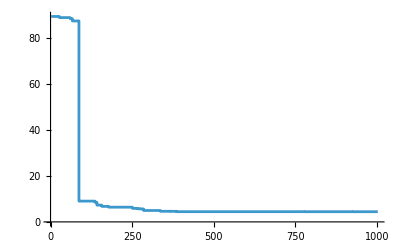

```mathematica
ListStepPlot[evo[[All, -1]], PlotRange->All]
```

#### Starting from single cell sin wave k = 2 r = 2

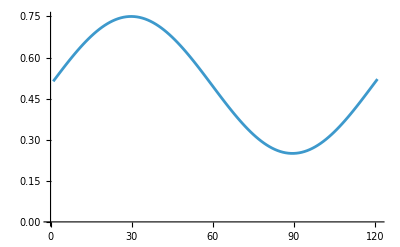

```mathematica
ListLinePlot[Table[1/4Sin[i/19]+1/2, {i, 1, 121}]]
```

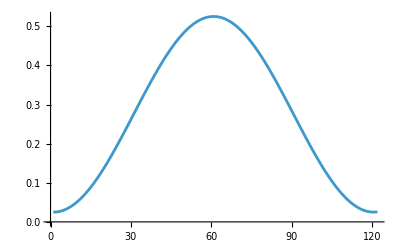

```mathematica
ListLinePlot[Table[1/4Sin[i/19]+.275, {i, -30, 91}]]
```

```mathematica
evo = Module[
{deep = 4000, width = 200, length = 120(*,initru, nru, nfit, inits*)},
SeedRandom[3532127];
initru = {ResourceFunction["RandomCA"][{2, 2}, "Quiescent"->True]["RuleNumber"], 2, 2};
sc = Table[1/4Sin[i/19]+.275, {i, -30, 91}];
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
nfit =Total[MapIndexed[Abs[sc[[First[#2]]]- Count[#, 1]/200]&, CellularAutomaton[nru, CenterArray[Table[1, 1], width], length]]];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]];
```

```mathematica
ArrayPlot[CellularAutomaton[#,CenterArray[Table[1, 1], 200], 120]]&/@ GatherBy[evo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[Prepend[{Count[#, 1]/200&/@CellularAutomaton[#,CenterArray[Table[1, 1], 200], 120]}, sc], PlotRange->All]&/@ GatherBy[evo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListStepPlot[evo[[All, -1]]]
```

-Graphics-

#### Other simple initial conditions

```mathematica
ListLinePlot[Table[1/4Sin[i/19]+1/2, {i, 1, 121}]]
```

-Graphics-

```mathematica
evo = Module[
{deep = 4000, width = 200, length = 120(*,initru, nru, nfit, inits*)},
SeedRandom[3532128];
initru = {ResourceFunction["RandomCA"][{2, 2}, "Quiescent"->True]["RuleNumber"], 2, 2};
sc = Table[1/4Sin[i/19]+1/2, {i, 1, 121}];
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
nfit =Total[MapIndexed[Abs[sc[[First[#2]]]- Count[#, 1]/200]&, CellularAutomaton[nru, CenterArray[Table[1, 50], width], length]]];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]];
```

```mathematica
ArrayPlot[CellularAutomaton[#,CenterArray[Table[1, 50], 200], 120]]&/@ GatherBy[evo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[Prepend[{Count[#, 1]/200&/@CellularAutomaton[#,CenterArray[Table[1, 50], 200], 120]}, sc], PlotRange->All]&/@ GatherBy[evo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListStepPlot[evo[[All, -1]]]
```

-Graphics-

```mathematica
evo = Module[
{deep = 4000, width = 200, length = 120(*,initru, nru, nfit, inits*)},
SeedRandom[3532128];
initru = {ResourceFunction["RandomCA"][{2, 2}, "Quiescent"->True]["RuleNumber"], 2, 2};
sc = Table[1/4Sin[i/19]+1/2, {i, 1, 121}];
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
nfit =Total[MapIndexed[Abs[sc[[First[#2]]]- Count[#, 1]/200]&, CellularAutomaton[nru, CenterArray[Table[1, 100], width], length]]];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]];
```

```mathematica
ArrayPlot[CellularAutomaton[#,CenterArray[Table[1, 100], 200], 120]]&/@ GatherBy[evo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[Prepend[{Count[#, 1]/200&/@CellularAutomaton[#,CenterArray[Table[1, 100], 200], 120]}, sc], PlotRange->All]&/@ GatherBy[evo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListStepPlot[evo[[All, -1]]]
```

-Graphics-

#### Longer length

```mathematica
ListLinePlot[Table[1/4Sin[i/19]+1/2, {i, 1, 121}]]
```

-Graphics-

```mathematica
evo = Module[
{deep = 2000, width = 200, length = 240(*,initru, nru, nfit, inits*)},
SeedRandom[3532128];
initru = {ResourceFunction["RandomCA"][{2, 2}, "Quiescent"->True]["RuleNumber"], 2, 2};
sc = Table[1/4Sin[i/19]+1/2, {i, 1, 241}];
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
nfit =Total[MapIndexed[Abs[sc[[First[#2]]]- Count[#, 1]/200]&, CellularAutomaton[nru, RandomInteger[1, width], length]]];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]];
```

```mathematica
ArrayPlot[CellularAutomaton[#,RandomInteger[1, 200], 240]]&/@ GatherBy[evo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[Prepend[{Count[#, 1]/200&/@CellularAutomaton[#,RandomInteger[1, 200], 240]}, sc], PlotRange->All]&/@ GatherBy[evo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[Table[1/4Sin[i/19]+1/2, {i, 1, 121}]]
```

-Graphics-

```mathematica
evo = Module[
{deep = 2000, width = 200, length = 240(*,initru, nru, nfit, inits*)},
SeedRandom[3532128];
initru = {ResourceFunction["RandomCA"][{2, 2}, "Quiescent"->True]["RuleNumber"], 2, 2};
sc = Table[1/4Sin[i/19]+1/2, {i, 1, 121}];
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
nfit =Total[MapIndexed[Abs[sc[[First[#2]]]- Count[#, 1]/200]&, CellularAutomaton[nru, RandomInteger[1, width], {{120, length}}]]];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]];
```

```mathematica
ArrayPlot[CellularAutomaton[#,RandomInteger[1, 200], 240]]&/@ GatherBy[evo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[Prepend[{Count[#, 1]/200&/@CellularAutomaton[#,RandomInteger[1, 200], {{120, 240}}]}, sc], PlotRange->All]&/@ GatherBy[evo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Longer length from random

```mathematica
evo = Module[
{deep = 2000, width = 200, length = 240(*,initru, nru, nfit, inits*)},
SeedRandom[3532129];
initru = {ResourceFunction["RandomCA"][{2, 2}, "Quiescent"->True]["RuleNumber"], 2, 2};
sc = Table[1/4Sin[i/19]+1/2, {i, 1, 241}];
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
nfit =Total[MapIndexed[Abs[sc[[First[#2]]]- Count[#, 1]/200]&, CellularAutomaton[nru, RandomInteger[1, width], length]]];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]];
```

```mathematica
ArrayPlot[CellularAutomaton[#,RandomInteger[1, 200], 240]]&/@ GatherBy[evo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[Prepend[{Count[#, 1]/200&/@CellularAutomaton[#,RandomInteger[1, 200], 240]}, sc], PlotRange->All]&/@ GatherBy[evo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Derivative of sin wave

```mathematica
ListLinePlot[{Differences[#], #}&@Table[2Sin[i/19]+1/2, {i, 1, 120}]]
```

-Graphics-